Linear Example

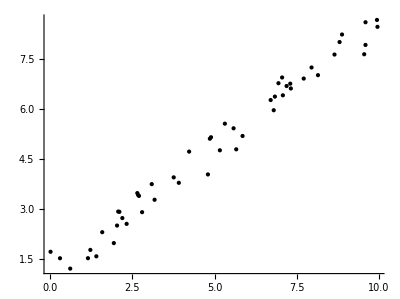

```mathematica
a=.75;
b=1.112;
line[x_]:=a*x+b
xdat=RandomReal[{0,10},50];
ydat=(line /@ xdat)+RandomReal[{-.7,.7},50];
Graphics[Point[Transpose[{xdat,ydat}]], Axes->True]
```

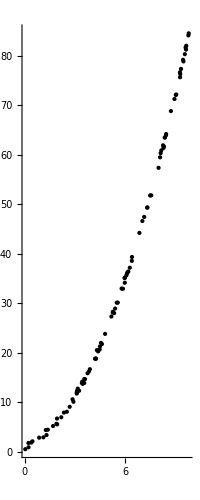

```mathematica
a=.75;
b=1.112;
line[x_]:=a*x^2+b*x+b
xdat=RandomReal[{0,10},100];
ydat=(line /@ xdat)+RandomReal[{-.7,.7},100];
Graphics[Point[Transpose[{xdat,ydat}]], Axes->True]
```

```mathematica
aa=Transpose[{ConstantArray[1,100],xdat,#^2&/@xdat}]

approx=LeastSquares[aa,ydat]
```

{{1,0.232412,0.0540153},{1,0.228576,0.0522472},{1,8.3824,70.2646},{1,5.8742,34.5062},{1,4.49985,20.2487},{1,3.14375,9.88315},{1,9.46998,89.6805},{1,4.80907,23.1271},{1,5.99291,35.915},{1,9.28849,86.2761},{1,5.98592,35.8312},{1,6.11509,37.3943},{1,3.56126,12.6826},{1,9.65844,93.2854},{1,1.30872,1.71274},{1,3.83587,14.7139},{1,6.85936,47.0509},{1,1.38817,1.92701},{1,9.34539,87.3364},{1,5.40953,29.263},{1,3.12439,9.76179},{1,8.37298,70.1068},{1,2.91617,8.50407},{1,5.26606,27.7313},{1,6.19553,38.3845},{1,4.25366,18.0936},{1,4.20556,17.6867},{1,5.79526,33.5851},{1,9.03434,81.6193},{1,8.09407,65.5139},{1,4.56289,20.82},{1,0.0386014,0.00149007},{1,4.25995,18.1471},{1,9.48846,90.0308},{1,4.61871,21.3325},{1,5.56768,30.9991},{1,7.56614,57.2464},{1,8.00409,64.0655},{1,7.33824,53.8497},{1,9.06045,82.0918},{1,1.6992,2.8873},{1,8.45496,71.4864},{1,9.57181,91.6196},{1,3.90004,15.2103},{1,3.15715,9.96762},{1,6.4146,41.147},{1,7.0357,49.5011},{1,7.49919,56.2378},{1,6.07698,36.9297},{1,9.78472,95.7408},{1,8.95421,80.1779},{1,9.61732,92.4929},{1,4.39185,19.2884},{1,4.31698,18.6363},{1,2.19083,4.79976},{1,1.2655,1.60149},{1,3.41964,11.6939},{1,1.93531,3.74544},{1,8.44871,71.3808},{1,5.50472,30.3019},{1,3.25386,10.5876},{1,8.29601,68.8238},{1,7.32334,53.6313},{1,8.74088,76.4031},{1,7.14633,51.07},{1,2.52464,6.37379},{1,2.69217,7.24778},{1,9.80589,96.1554},{1,3.76029,14.1398},{1,8.32277,69.2685},{1,0.866544,0.750899},{1,3.45229,11.9183},{1,6.14719,37.7879},{1,2.86477,8.20692},{1,8.1687,66.7277},{1,5.27427,27.818},{1,1.94759,3.79309},{1,9.29933,86.4776},{1,4.48306,20.0979},{1,0.467841,0.218876},{1,9.64689,93.0625},{1,9.27946,86.1083},{1,3.17502,10.0807},{1,6.40565,41.0324},{1,3.47131,12.05},{1,1.90253,3.61963},{1,3.56747,12.7268},{1,6.285,39.5012},{1,3.12309,9.75371},{1,3.48752,12.1628},{1,5.3488,28.6097},{1,8.27212,68.428},{1,0.398661,0.15893},{1,1.12111,1.25689},{1,5.97166,35.6608},{1,3.604,12.9888},{1,2.34982,5.52167},{1,5.18397,26.8736},{1,3.11316,9.69177},{1,8.12859,66.0739}}

{1.1252,1.07061,0.755231}

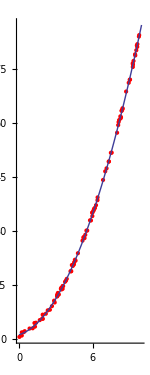

```mathematica
Show[Graphics[{Red,Point[Transpose[{xdat,ydat}]]}, Axes->True],Plot[approx[[1]]+approx[[2]]x+approx[[3]]x^2,{x,0,10}]]
```

Periodic Example

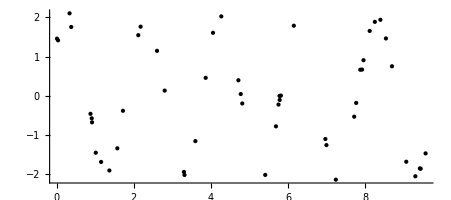

```mathematica
d=1.221;
e=1.557;
fun[x_]:=d*Cos[Pi*x]+e*Sin[Pi*x]
xdat2=RandomReal[{0,10},50];
ydat2=(fun /@ xdat2)+RandomReal[{-.2,.2},50];
Graphics[Point[Transpose[{xdat2,ydat2}]], Axes->True]
```

```mathematica
aaa={Cos[Pi #],Sin[Pi #]}&/@ xdat2;
approx=LeastSquares[aaa,ydat2]
```

{1.22531,1.52432}

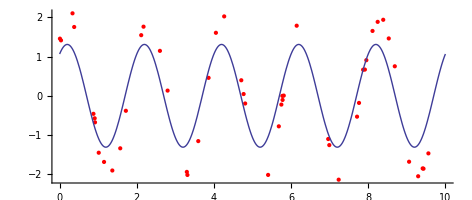

```mathematica
Show[Graphics[{Red,Point[Transpose[{xdat2,ydat2}]]}, Axes->True],Plot[approx[[1]]Cos[Pi*x]+approx[[2]]Sin[Pi*x],{x,0,10}]]
```

Non-Linear Example

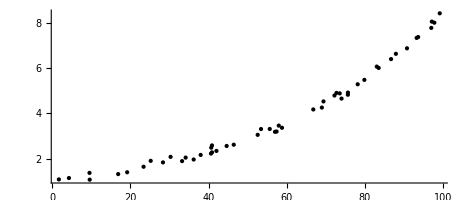

```mathematica
r=.0213;
fun2[x_]:=Exp[r*x]
xdat3=RandomReal[{0,100},50];
ydat3=(fun2 /@ xdat3)+RandomReal[{-.2,.2},50];
Graphics[Point[Transpose[{xdat3,ydat3}]], Axes->True,AxesOrigin->{0,0}]
```